Input GPDs

```mathematica
vπ[x_]:=0.838*x^(0.7-1)(1-x)^2.03(1+13.8 x^2)
```

```mathematica
h[β_,α_]:=Gamma[2b+2]/(2^(2b+1)Gamma[b+1]^2)*(((1-Abs[β])^2-α^2)^b)/(1-Abs[β])^(2b+1)/.b->2
```

Input for D term in ERBL region(|x|<ξ)

```mathematica
q0[x_,ξ_,t_]:=-0.793/((1+t/190^2)^3)*(x/ξ)*(1-(x/ξ)^2)
```

Input for GPD in the ERBL region(|x|<ξ)

```mathematica
q1[x_,ξ_,t_]:=1/(1+t/6870)(NIntegrate[(h[β,(x-β)/ξ]*vπ[β])/ξ,{β,0,(x+ξ)/(1+ξ)}])
```

Input for GPD in the DGLAP region(x>ξ)

```mathematica
q2[x_,ξ_,t_]:=1/(1+t/6870)NIntegrate[(h[β,(x-β)/ξ]*vπ[β])/ξ,{β,(x-ξ)/(1-ξ),(x+ξ)/(1+ξ)},WorkingPrecision->10]
```

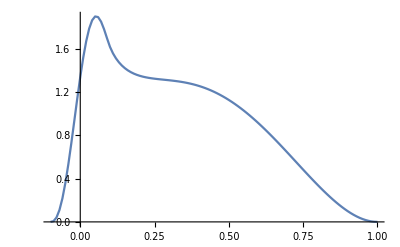

```mathematica
ListLinePlot@Transpose[{Join[Range[-ξ3,ξ3,0.01],Range[ξ3,1,0.01]],Join[Table[q1[x,ξ3,0],{x,-ξ3,ξ3,0.01}],Table[q2[x,ξ3,0],{x,ξ3,1,0.01}]]}]
```

Iuput GDA

```mathematica
DA[x_,ξ_,t_]:=1/(1+t/6870)*6x(1-x)*(2ξ-1)
```